```mathematica
T = {{Exp[β* J+ β*h], Exp[-β*J]}, {Exp[-β*J], Exp[β*J - β*h]}}
```

{{ⅇ^(h β+J β),ⅇ^(-J β)},{ⅇ^(-J β),ⅇ^(-h β+J β)}}

```mathematica
MatrixForm[%]
```

(ⅇ^(h β+J β) | ⅇ^(-J β)
ⅇ^(-J β) | ⅇ^(-h β+J β))

```mathematica
RT = Eigenvectors[T]
```

{{1/2 ⅇ^(-h β) (-ⅇ^(2 J β)+ⅇ^(2 h β+2 J β)-√(4 ⅇ^(2 h β)+ⅇ^(4 J β)-2 ⅇ^(2 h β+4 J β)+ⅇ^(4 h β+4 J β))),1},{1/2 ⅇ^(-h β) (-ⅇ^(2 J β)+ⅇ^(2 h β+2 J β)+√(4 ⅇ^(2 h β)+ⅇ^(4 J β)-2 ⅇ^(2 h β+4 J β)+ⅇ^(4 h β+4 J β))),1}}

```mathematica
la = Eigenvalues[T]
```

{1/2 ⅇ^(-h β-J β) (ⅇ^(2 J β)+ⅇ^(2 h β+2 J β)-√(4 ⅇ^(2 h β)+ⅇ^(4 J β)-2 ⅇ^(2 h β+4 J β)+ⅇ^(4 h β+4 J β))),1/2 ⅇ^(-h β-J β) (ⅇ^(2 J β)+ⅇ^(2 h β+2 J β)+√(4 ⅇ^(2 h β)+ⅇ^(4 J β)-2 ⅇ^(2 h β+4 J β)+ⅇ^(4 h β+4 J β)))}

```mathematica
T1=T-IdentityMatrix[2]*la[[2]]
```

{{ⅇ^(h β+J β)-1/2 ⅇ^(-h β-J β) (ⅇ^(2 J β)+ⅇ^(2 h β+2 J β)+√(4 ⅇ^(2 h β)+ⅇ^(4 J β)-2 ⅇ^(2 h β+4 J β)+ⅇ^(4 h β+4 J β))),ⅇ^(-J β)},{ⅇ^(-J β),ⅇ^(-h β+J β)-1/2 ⅇ^(-h β-J β) (ⅇ^(2 J β)+ⅇ^(2 h β+2 J β)+√(4 ⅇ^(2 h β)+ⅇ^(4 J β)-2 ⅇ^(2 h β+4 J β)+ⅇ^(4 h β+4 J β)))}}

```mathematica
MatrixForm[%]
```

(ⅇ^(h β+J β)-1/2 ⅇ^(-h β-J β) (ⅇ^(2 J β)+ⅇ^(2 h β+2 J β)+√(4 ⅇ^(2 h β)+ⅇ^(4 J β)-2 ⅇ^(2 h β+4 J β)+ⅇ^(4 h β+4 J β))) | ⅇ^(-J β)
ⅇ^(-J β) | ⅇ^(-h β+J β)-1/2 ⅇ^(-h β-J β) (ⅇ^(2 J β)+ⅇ^(2 h β+2 J β)+√(4 ⅇ^(2 h β)+ⅇ^(4 J β)-2 ⅇ^(2 h β+4 J β)+ⅇ^(4 h β+4 J β))))

```mathematica
RowReduce[T1]
```

{{1,-1/2 ⅇ^(-h β) (-ⅇ^(2 J β)+ⅇ^(2 h β+2 J β)+√(4 ⅇ^(2 h β)+ⅇ^(4 J β)-2 ⅇ^(2 h β+4 J β)+ⅇ^(4 h β+4 J β)))},{0,0}}

```mathematica
R = Transpose[RT]
```

{{1/2 ⅇ^(-h β) (-ⅇ^(2 J β)+ⅇ^(2 h β+2 J β)-√(4 ⅇ^(2 h β)+ⅇ^(4 J β)-2 ⅇ^(2 h β+4 J β)+ⅇ^(4 h β+4 J β))),1/2 ⅇ^(-h β) (-ⅇ^(2 J β)+ⅇ^(2 h β+2 J β)+√(4 ⅇ^(2 h β)+ⅇ^(4 J β)-2 ⅇ^(2 h β+4 J β)+ⅇ^(4 h β+4 J β)))},{1,1}}

```mathematica
MatrixForm[R]
```

(1/2 ⅇ^(-h β) (-ⅇ^(2 J β)+ⅇ^(2 h β+2 J β)-√(4 ⅇ^(2 h β)+ⅇ^(4 J β)-2 ⅇ^(2 h β+4 J β)+ⅇ^(4 h β+4 J β))) | 1/2 ⅇ^(-h β) (-ⅇ^(2 J β)+ⅇ^(2 h β+2 J β)+√(4 ⅇ^(2 h β)+ⅇ^(4 J β)-2 ⅇ^(2 h β+4 J β)+ⅇ^(4 h β+4 J β)))
1 | 1)

```mathematica
MatrixForm[Inverse[R]]
```

(-ⅇ^(h β)/(√(4 ⅇ^(2 h β)+ⅇ^(4 J β)-2 ⅇ^(2 h β+4 J β)+ⅇ^(4 h β+4 J β))) | (-ⅇ^(2 J β)+ⅇ^(2 h β+2 J β)+√(4 ⅇ^(2 h β)+ⅇ^(4 J β)-2 ⅇ^(2 h β+4 J β)+ⅇ^(4 h β+4 J β)))/(2 √(4 ⅇ^(2 h β)+ⅇ^(4 J β)-2 ⅇ^(2 h β+4 J β)+ⅇ^(4 h β+4 J β)))
ⅇ^(h β)/(√(4 ⅇ^(2 h β)+ⅇ^(4 J β)-2 ⅇ^(2 h β+4 J β)+ⅇ^(4 h β+4 J β))) | -(-ⅇ^(2 J β)+ⅇ^(2 h β+2 J β)-√(4 ⅇ^(2 h β)+ⅇ^(4 J β)-2 ⅇ^(2 h β+4 J β)+ⅇ^(4 h β+4 J β)))/(2 √(4 ⅇ^(2 h β)+ⅇ^(4 J β)-2 ⅇ^(2 h β+4 J β)+ⅇ^(4 h β+4 J β))))

```mathematica
RInv={{1/(E^(β*J)(2Q)), 1 - SubPlus[λ']/(2Q)},{-1/(E^(β*J)(2Q)),SubPlus[λ']/(2Q)}}//MatrixForm
```

(ⅇ^(-J β)/(2 Q) | 1-((λ')_+)/(2 Q)
-ⅇ^(-J β)/(2 Q) | ((λ')_+)/(2 Q))

```mathematica
Ts = {{SubPlus[λ],0},{0,SubMinus[λ]}};
```

1.Z=∑R*Ts^(N-1)*R^-1(σ1,σN)

```mathematica
2. SubMinus[λ']=E^(β*J)*Sinh[β*h]-Q
3. SubPlus[λ']=E^(β*J)*Sinh[β*h]+Q
4. SubMinus[λ]= E^(β*J)*Cosh[β*h]-Q
5. SubPlus[λ]= E^(β*J)*Cosh[β*h]+Q
6. Q = √(E^(2*β*J)*Cosh[β*h]^2-2Sinh[2*β*J])
```

```mathematica
Z=SubPlus[λ]^(n-1)*(E^(β*h)*SubPlus[λ']/(2Q)+1/(E^βJ 2Q)-E^-βh*(SubMinus[λ]')/(2Q))-SubMinus[λ]^(n-1)*(E^(β*h)*SubPlus[λ']/(2Q)+1/(E^βJ 2Q)- E^-βh*(SubPlus[λ]')/(2Q))
```

```mathematica
Итог:
Subscript[(F/N), N->∞]≈ -Subscript[k, B]*T*ln(SubPlus[λ])
```

## h = 0: Найдём ⟨H⟩:

```mathematica
H=(-J*∑)_(j=1)^(n-1)Subscript[σ, j] Subscript[σ, j+1];
```

```mathematica
Subscript[Z, j] = 2Cosh[β*J] ⇒ Z = 2(2Cosh[β*J])^(n-1)
```

Можно ли искать вместо намагниченности одного спина "намагниченность" двух τ_j=σ_(j-1)*σ_j??

Если да, то:

```mathematica
<m> = <τ> = (< T >)/N ,где 
<T> = 1/Z∑T*Exp[-β*-J*T]
T=∑Subscript[σ, j] Subscript[σ, j+1]
```

Рассмотрим  (δ(Log[Z]))/δJ:

```mathematica
= 1/Z*δ/δJ*(∑Exp[β*J*T])=1/Z*∑β*T*Exp[β*J*T]
```

```mathematica
Таким образом: <T> = (δ(Log[Z]))/δJ*1/β=1/(2^N Cosh[β*J]^(N-1))*1/β*2^N*(N-1)Cosh[β*J]^(N-2)*β*Sinh[β*J] 
 = (N-1)Tanh[β*J]
```

```mathematica
Следовательно, <τ>_(N->∞)= (N-1)/N Tanh[β*J]≈ Tanh[β*J]
```

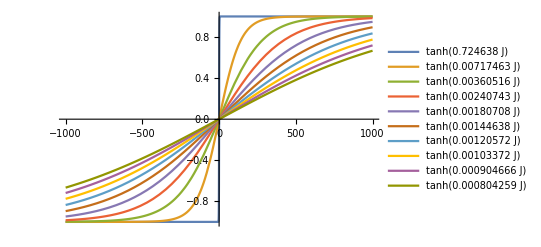

```mathematica
Plot[Evaluate[Table[Tanh[J/(k T)],{T,1,1000,200}]],{J,-1000,1000},PlotLegends->"Expressions"]
```

```mathematica
k=1.38;
```

В данном случае при стремлении значения к -1, кол-во смен знака спина стремится к максимуму, и следовательно < σ > -> 0
Однако при стремлении значения к 1, кол-во смен знака уменьшается, но определить < σ > не удастся, т.к. в зависимости от положения хотя бы одной смены в цепи среднее значение может быть как 0, так и ±1.

```mathematica
Энергия цепи в таком случае будет равна  ⟨H⟩ = -J*⟨T⟩ = -J*(N-1)*Tanh[β*J]=-J(N-1)Tanh[J/(Subscript[k, B] T)]
Теплоёмкость на спин будет Subscript[( (δE(=δ⟨H⟩))/δT), N]*1/N=-J*((N-1)/N)*Sech[J/(Subscript[k, B] T)]^2*-J/(Subscript[k, B] T^2)=(N->∞)=J^2/(Subscript[k, B] T^2)*Sech[J/(Subscript[k, B] T)]^2
```

```mathematica
k=1.38
```

1.38

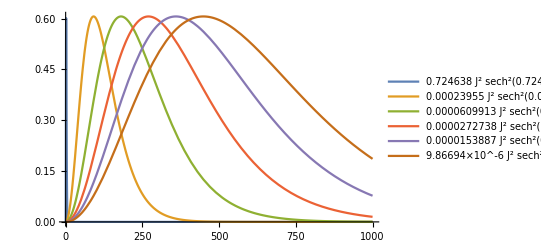

```mathematica
Plot[Evaluate[Table[J^2/(k*T^2)*Sech[J/(k*T)]^2,{T,1,273,54}]],{J,0,1000},PlotLegends->"Expressions"]
```

Найдём первую поправку разницы между энергией периодичной и открытой систем в общем случае

```mathematica
Z1=λp^n + λm^n;
λp= E^(β*J)*Cosh[β*h]+Q;
λm = E^(β*J)*Cosh[β*h]-Q;

Q = √(E^(2*β*J)*Cosh[β*h]^2-2Sinh[2*β*J]);
```

```mathematica
Expand[Z1]
```

(ⅇ^(J β) Cosh[h β]-√(ⅇ^(2 J β) Cosh[h β]^2-2 Sinh[2 J β]))^n+(ⅇ^(J β) Cosh[h β]+√(ⅇ^(2 J β) Cosh[h β]^2-2 Sinh[2 J β]))^n

```mathematica
Z2=λp^(n-1)(E^(β*J)*λp2 + 1)^2+λm^(n-1)(E^(β*J)*λm2+1)^2;
λp2=E^(β*J)*Sinh[β*h]+Q;
λm2=E^(β*J)*Sinh[β*h]+-Q;
```

Для начала найдём формулу средней энергии:

```mathematica
⟨U⟩=⟨H⟩=1/Z∑H*Exp[-β*H];
```

С другой стороны:

```mathematica
(δ(Log[Z]))/δβ=1/Z*δ/δβ(∑Exp[-β*H])=1/Z*∑-H*Exp[-β*H]
```

Следовательно,

```mathematica
⟨U⟩=-(δ(Log[Z]))/δβ
```

Перейдём к нашей задаче:

```mathematica
⟨Subscript[U, PBC]⟩-⟨Subscript[U, OBC]⟩=(-δ(Log[Z1]))/δβ+(δ(Log[Z2]))/δβ=-(δ(Log[Z1]-Log[Z2]))/δβ=-(δ(Log[Z1/Z2]))/δβ
```

Вытащив из обоих статсумм λp, получим:

```mathematica
Z1/Z2=(λp(1+(λm/λp)^N))/((E^(β*J)*λp2+1)^2(1+(λm/λp)^(N-1)((E^(β*J)*λm2 +1)/(E^(β*J)*λp2 + 1))^2))
```

Поправка для разности свободных энергий:

```mathematica
F1=-Subscript[k, B]*T*Log[Z1]=-Subscript[k, B]*T*n*Log[λp]-Subscript[k, B] T*Log[1+(λm/λp)^n]=-Subscript[k, B]*T*n*Log[λp]-Subscript[k, B]*T*(λm/λp)^n-o((λm/λp)^n)
F2=-Subscript[k, B]*T*Log[Z2]=-Subscript[k, B]*T*((n-1)*Log[λp]+2*Log[E^(β*J)*λp2+1]+(λm/λp)^(n-1)*((E^(β*J)*λm2+1)/(E^(β*J)*λp2+1))^2+o((λm/λp)^(n-1)))
```

```mathematica
F2-F1=-Subscript[k, B]*T*(-Log[λp]+2*Log[E^(β*J)*λp2+1]+(λm/λp)^(n-1)(((E^(β*J)*λm2+1)/(E^(β*J)*λp2+1))^2-λm/λp)+o((λm/λp)^(n-1)))=
=-Subscript[k, B]*T*(-Log[λp]+2*Log[E^(β*J)*λp2+1]+O[(λm/λp)^(n-1)])
```

А при n→∞:

```mathematica
≈-Subscript[k, B]*T*Log[((E^(β*J)*λp2+1)^2)/λp]
```

30.09.2020

```mathematica
λp= E^(β*J)*Cosh[β*h]+Q;
λm = E^(β*J)*Cosh[β*h]-Q;
Q = √(E^(2*β*J)*Cosh[β*h]^2-2Sinh[2*β*J]);
```

```mathematica
Clear[h]
```

```mathematica
A[β_,h_,J_] =((E^(β*J)Sinh[β*h]^2)/Q+1/(E^(β*J)Q)+Cosh[β*h]);
```

```mathematica
Simplify[A[β,0,J]]
```

1+ⅇ^(J β) √(ⅇ^(-2 J β))

```mathematica
Ab[β_,h_,J_]=D[A[β,h,J],β]
```

h Sinh[h β]-(ⅇ^(-J β) (2 ⅇ^(2 J β) J Cosh[h β]^2-4 J Cosh[2 J β]+2 ⅇ^(2 J β) h Cosh[h β] Sinh[h β]))/(2 (ⅇ^(2 J β) Cosh[h β]^2-2 Sinh[2 J β])^(3/2))-(ⅇ^(J β) Sinh[h β]^2 (2 ⅇ^(2 J β) J Cosh[h β]^2-4 J Cosh[2 J β]+2 ⅇ^(2 J β) h Cosh[h β] Sinh[h β]))/(2 (ⅇ^(2 J β) Cosh[h β]^2-2 Sinh[2 J β])^(3/2))-(ⅇ^(-J β) J)/(√(ⅇ^(2 J β) Cosh[h β]^2-2 Sinh[2 J β]))+(2 ⅇ^(J β) h Cosh[h β] Sinh[h β])/(√(ⅇ^(2 J β) Cosh[h β]^2-2 Sinh[2 J β]))+(ⅇ^(J β) J Sinh[h β]^2)/(√(ⅇ^(2 J β) Cosh[h β]^2-2 Sinh[2 J β]))

```mathematica
Simplify[Ab[β,0,J]]
```

0

```mathematica
Addp[β_,h_,J_]=D[Ab[β,h,J],β];
```

```mathematica
Simplify[Addp[β,0,J]]
```

0

```mathematica
Am[β_,h_,J_] =((E^(β*J)Sinh[β*h]^2)/Q+1/(E^(β*J)Q)+Cosh[β*h]);
Addm[β_,h_,J_]=D[D[Am[β,h,J],β],β];
```

```mathematica
Simplify[Addm[β,0,J]]
```

0

21.10.2020 (поиск X)

```mathematica
Q[bj_,bh_] := √(E^(2*bj)*Cosh[bh]^2-2Sinh[2*bj]);
```

```mathematica
lp[bj_,bh_]:= E^bj*Cosh[bh]+Q[bj,bh];
lm[bj_,bh_] := E^(bj)*Cosh[bh]-Q[bj,bh];
Ap[bj_,bh_] :=((E^(bj)Sinh[bh]^2)/Q[bj,bh]+1/(E^(bj)Q[bj,bh])+Cosh[bh]);
Am[bj_,bh_] :=((E^(bj)Sinh[bh]^2)/Q[bj,bh]+1/(E^(bj)Q[bj,bh])-Cosh[bh]);
```

```mathematica
Zobc[bj_,bh_]:=lp[bj,bh]^(n-1)Ap[bj,bh]-lm[bj,bh]^(n-1)Am[bj,bh];
```

Как мы знаем:
⟨ m ⟩ = 1/(Z*b)dZ/dh= 1/Z dZ/(d(bh))
Тогда
x = (d<m>)/(d<h>)|(h->0) = (d<m>)/(d(bh))| (bh→0) =b ((d^2 Z)/(d(bh))^2- (dZ/(d(bh)))^2)| (bh→0)

```mathematica
D[Zobc[bj,bh],bh]/.bh->0
```

0

Поэтому
x = b(d^2 Z)/(d(bh))^2| (bh→0)

```mathematica
Zobc[bj,0]//Simplify
```

(ⅇ^bj-√(ⅇ^(-2 bj)))^(-1+n)+(ⅇ^bj+√(ⅇ^(-2 bj)))^(-1+n)+ⅇ^bj √(ⅇ^(-2 bj)) (-(ⅇ^bj-√(ⅇ^(-2 bj)))^(-1+n)+(ⅇ^bj+√(ⅇ^(-2 bj)))^(-1+n))

```mathematica
D[D[Zobc[bj,bh],bh],bh]/Zobc[bj,bh]/.bh->0//Simplify
```

(((ⅇ^bj+√(ⅇ^(-2 bj)))^(-1+n) (2 ⅇ^bj-ⅇ^(3 bj)+√(ⅇ^(-2 bj))))/(√(ⅇ^(-2 bj)))+(ⅇ^(2 bj) (ⅇ^bj-√(ⅇ^(-2 bj)))^n (-2 ⅇ^bj+ⅇ^(3 bj)+√(ⅇ^(-2 bj))))/(-1+ⅇ^(3 bj) √(ⅇ^(-2 bj)))-ⅇ^(2 bj) (ⅇ^bj-√(ⅇ^(-2 bj)))^(-1+n) (-1+ⅇ^bj √(ⅇ^(-2 bj))) (-1+n)+ⅇ^(2 bj) (ⅇ^bj+√(ⅇ^(-2 bj)))^(-1+n) (1+ⅇ^bj √(ⅇ^(-2 bj))) (-1+n))/((ⅇ^bj-√(ⅇ^(-2 bj)))^(-1+n)+(ⅇ^bj+√(ⅇ^(-2 bj)))^(-1+n)+ⅇ^bj √(ⅇ^(-2 bj)) (-(ⅇ^bj-√(ⅇ^(-2 bj)))^(-1+n)+(ⅇ^bj+√(ⅇ^(-2 bj)))^(-1+n)))

Что при упрощении даёт

```mathematica
X[bj_] := (1/2 + n*E^(2*bj)-E^(4*bj)/2 +1/2 Tanh[bj]^(n-1)(E^(4*bj)-2 E^(2bj)+1))*b
```

Так как получилась небезразмерная величина, умножим на j

Чтобы показать обратную зависимость от T, учитывая, что bj = f(1/T), вместо bj подставим 1/bj

```mathematica
Manipulate[Plot[(1/2 + n*E^(2*1/bj)-E^(4*1/bj)/2 +1/2 Tanh[1/bj]^(n-1)(E^(4*1/bj)-2 E^(2/bj)+1))1/bj,{bj,0,1000},PlotRange->{{0,10},Full}],{n,1,100000,1}]
```

General::munfl: 0.771432^99999 is too small to represent as a normalized machine number; precision may be lost.

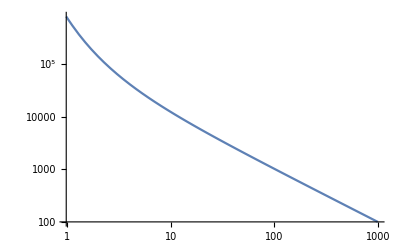

```mathematica
LogLogPlot[(1/2 + n*E^(2*1/bj)-E^(4*1/bj)/2 +1/2 Tanh[1/bj]^(n-1)(E^(4*1/bj)-2 E^(2/bj)+1))*1/bj/.n->100000,{bj,0,1000}]
```

Это показывает обратно пропорциональную зависимость X от T

Расчеты дробей вида (1 + tanh^(n-4))/(1 + tanh^n) из формулы теплоёмкости на спин

```mathematica
Y[bj_]:= (1+(Tanh[bj])^(n-4))/(1 + (Tanh[bj])^(n))
Manipulate[Plot[(1+(Tanh[bj])^(n-4))/(1 + (Tanh[bj])^(n)),{bj,0,10}, PlotRange->All],{n,4,1000,10}]
```

General::munfl: 0.000204286^996 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.000204286^1000 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.000204286^906 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.000204286^910 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.000204286^906 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.000204286^910 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Y1[bj_]:=((Sinh[bj])^(n-4)+(Cosh[bj])^(n-4))/((Sinh[bj])^n+(Cosh[bj])^n)*(Cosh[bj])^4
Y1[0]
D[Y1[bj],bj]/.bj->0
D[D[Y1[bj],bj],bj]/.bj->0
```

(1+0^(-4+n))/(1+0^n)

(0 (1+0^(-4+n)))/(1+0^n)+(0^(-5+n) (-4+n))/(1+0^n)-(0^(-1+n) (1+0^(-4+n)) n)/((1+0^n)^2)

```mathematica
(4 (1+0^(-4+n)))/(1+0^n)+(0^(-4+n) (-4+n))/(1+0^n)+(0^n (1+0^(-4+n)) n)/((1+0^n)^2)-(2 0^(-6+2 n) (-4+n) n)/((1+0^n)^2)+(2 0^(-2+2 n) (1+0^(-4+n)) n^2)/((1+0^n)^3)+(-4+0^(-4+n) (-4+n)+0^(-6+n) (-5+n) (-4+n)+n)/(1+0^n)-((1+0^(-4+n)) (n+0^n n+0^(-2+n) (-1+n) n))/((1+0^n)^2)=0
```

```mathematica
(0 (1+0^(-4+n)))/(1+0^n)+(0^(-5+n) (-4+n))/(1+0^n)-(0^(-1+n) (1+0^(-4+n)) n)/((1+0^n)^2)=0
```

Итог: в ряде Тейлора от нуля единственный член - 1, зависимость от N ещё не найдена